```mathematica
(*state variables*)
vars={
R,(* root biomass  *)
S ,(* shoot biomass  *)
ρN,(* nitrogen sharing *)
ρC (* carbon sharing *)
};

(* Synthesizing Unit  *)
F[x_,y_]:=Min[x,y];

(*parameter values*)

R0=1;
S0=2;
β=.2;
αN=1;
αC=1;
ηR=1;
ηS=.2;
λ=100;
tmax=4.2;

(*assimilation rates*)

UN=αN R;
UC=αC S;

(*growth rate of root and shoot*)

dRdt=F[ρC,UN/ηR];
dSdt=F[UC,ρN/ηS];

(*targets for N and C shared (fast equilibria)*)

gρN=UN-ηR dRdt;
gρC=UC-dSdt;

(*ODEs: root and shoot biomass, shared N and C (buffered)*)

eqs=(#[[1]]==(#[[2]]/.(#->#[t]&/@vars)))&/@{
R'[t]==dRdt,
S'[t]==dSdt,
ρN'[t]==λ (gρN-ρN),
ρC'[t]==λ (gρC-ρC)
};
```

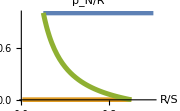
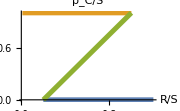

```mathematica
(*find fast steady states analytically*)
fluxsol=Quiet@NSolve[{ρN==gρN,ρC==gρC},{ρC,ρN}];
(*some style*)

fontfamily="Times";
style={LabelStyle->10,ImageSize->Small,PlotStyle->({#,Thickness[.02]}&/@(ColorData[97]/@{2,1,3})),LabelStyle->{FontFamily->fontfamily}};
(*bifurcations*)
Row[{(Export[NotebookDirectory[]<>"root-shoot-bifurcations-rhoN.pdf",#];#)&@Plot[Evaluate[(ρN/R) /.fluxsol/.S->1],{R,.01,1.2},AxesLabel->{Style["R/S",Italic]},PlotRange->Full,PlotLabel->Style["ρ_N/R",Italic],Evaluate@style],
(Export[NotebookDirectory[]<>"root-shoot-bifurcations-rhoC.pdf",#];#)&@Plot[Evaluate[(ρC/S) /.fluxsol/.S->1],{R,.01,1.2},AxesLabel->{Style["R/S",Italic]},PlotRange->Full,PlotLabel->Style["ρ_C/S",Italic],Evaluate@style]}]
```

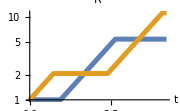
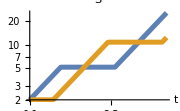
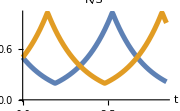
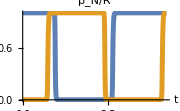
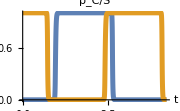

```mathematica
(*simulations*)
simulate[inis_]:=NDSolve[
{eqs,inis},
vars,
{t,0,tmax}
];
xmax=25;
style2={LabelStyle->12,ImageSize->Small,PlotStyle->Thickness[.025]};
(*solve the ODEs*)
sol1=
simulate[{
R[0]==R0,
S[0]==S0,
ρN[0]==αN R0,
ρC[0]==0
}];
sol2=simulate[{
R[0]==R0,
S[0]==S0,
ρN[0]==0,
ρC[0]==αC S0
}];
plotcols=ColorData[97]/@Range[2];
timeplotstyle={AxesOrigin->{0,0},ImageSize->Small,PlotStyle->({#,Thickness[.02]}&/@plotcols),AxesLabel->{"t"},LabelStyle->{FontFamily->fontfamily,FontSize->16}};
doplots[sols_]:=Style[Column[
{Row@Join[
Table[LogPlot[Evaluate[x[t]/.sols],{t,0,tmax},PlotLabel->(x/.{R->"StyleBox[\"R\",FontSlant->\"Italic\"]",S->"StyleBox[\"S\",FontSlant->\"Italic\"]"}),Evaluate@timeplotstyle,PlotRange->Automatic],{x,{R,S}}],
{Plot[Evaluate[{R[t]/S[t]}/.sols],{t,0,tmax},PlotLabel->"StyleBox[\"R\",FontSlant->\"Italic\"]StyleBox[\"/\",FontSlant->\"Italic\"]StyleBox[\"S\",FontSlant->\"Italic\"]",Evaluate@timeplotstyle,PlotRange->Automatic(*{0,maxSoverH}*)]}
],
Row@Table[Plot[Evaluate@Flatten@{Max[0,x]/.sols},{t,0,tmax},PlotLabel->Style[x/.{ρN[t]/R[t]->"SubscriptBox[\"ρ\", StyleBox[\"N\",FontSlant->\"Italic\"]]/R",ρC[t]/S[t]->"ρ_C/S"},Italic],Evaluate@timeplotstyle,PlotRange->Automatic(*{x/.{jCP->{0,1.05jCPm},jSG->{0,jSGm}}/.parvals}*)],{x,{ρN[t]/R[t],ρC[t]/S[t]}}]}
,Alignment->Center],LineBreakWithin->False];
(Export["root-shoot-simu.pdf",#];#)&@doplots[{sol1,sol2}]
```

```mathematica
(Export[NotebookDirectory[]<>"root-shoot-simulation-legend.pdf",#];#)&@Column[{
Style["Initializiation",FontFamily->fontfamily],
Grid[Table[Flatten@{Plot[1/2,{x,0,1},PlotRange->{0,1},PlotStyle->{Thickness[.15],plotcols[[i]]},Axes->None,ImageSize->20],Spacer[1],Style[#[[i]],FontFamily->fontfamily]&/@{{"ρ_N(0) = 1    ","ρ_N(0) = 0    "},{"ρ_C(0) = 0    ","ρ_C(0) = 1    "}}},{i,2}],Alignment->Left]},Alignment->Center]
```

Initializiation
-Graphics- |  | ρ_N(0) = 1     | ρ_C(0) = 0    
-Graphics- |  | ρ_N(0) = 0     | ρ_C(0) = 1